## Tau Soma Simulation Data Parser

```mathematica
imgSizer=650;
```

### ρ_qua bifurcation plot as gotten from the SPICE simulation of the Soma

In this section, the data was taken from the SPICE simulation of the Soma.  The IinVals and IlkVals were gotten from the measurements of the values set using the current sources.  In other words, they directly correspond to the value set on the bias side, but don’t necessarily match the value that is applied in the circuit, after it’s translated through any current mirror and/or has other leakages added to it.

```mathematica
IlkBase=338.994*10^-15;
IinVals={
312.485,263.568,228.627,202.443,182.096,
165.819,152.516,141.431,132.051,124.011,
117.055,110.968,105.597,100.823,96.5599,
92.7234,89.2524,86.0969,83.2231,80.5888
}*10^-15;
IlkVals={
IlkBase/0.5,IlkBase/0.6,IlkBase/0.7,IlkBase/0.8,IlkBase/0.9,
IlkBase/1.0,IlkBase/1.1,IlkBase/1.2,IlkBase/1.3,IlkBase/1.4,
IlkBase/1.5,IlkBase/1.6,IlkBase/1.7,IlkBase/1.8,IlkBase/1.9,
IlkBase/2.0,IlkBase/2.1,IlkBase/2.2,IlkBase/2.3,IlkBase/2.4};
dataVals=Transpose[{IinVals,0.5*IlkVals}];
dataVals⟦;;,1⟧/dataVals⟦;;,2⟧;
pQuaFitEq=Fit[dataVals,{x},x];
pQuaFitOffEq=Fit[dataVals,{1,x},x];
pQuaFitRules=FindFit[dataVals,m x,{m},x];
pQuaFitOffRules=FindFit[dataVals,mOff x+b,{mOff,b},x];
Print[Style["ρ_qua with no offset: ",Bold],m/.pQuaFitRules]
Print[Style["ρ_qua if offset is included: ",Bold],mOff/.pQuaFitOffRules]
Print[Style["Total Offset: ",Bold],UnitConvert[Quantity[b,"Amps"],"FemtoAmps"]/.pQuaFitOffRules]
Manipulate[
Show[
ListPlot[dataVals,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle⟦1⟧,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEq,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.3],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua with no offset: 1.02592

ρ_qua if offset is included: 1.1575

Total Offset: -22.5338

```mathematica
iInVals={.4609,.4665,.4721,.47775,.48345,.48915,.4949,.50065,.5064,.51215,.51795,.52375,.52955,.53535,.5412,.54705,.5529,.55875,.56465,.57055};
Differences[iInVals]
```

{0.0056,0.0056,0.00565,0.0057,0.0057,0.00575,0.00575,0.00575,0.00575,0.0058,0.0058,0.0058,0.0058,0.00585,0.00585,0.00585,0.00585,0.0059,0.0059}

```mathematica
Accumulate[{.4609,.0056,.0056,.00565,.0057,.00575,.00575,.00575,.00575,.00575,.00575,0.0058,0.0058,0.0058,0.00585,0.00585,0.00585,0.00585,0.0059,0.0059}]
```

{0.4609,0.4665,0.4721,0.47775,0.48345,0.4892,0.49495,0.5007,0.50645,0.5122,0.51795,0.52375,0.52955,0.53535,0.5412,0.54705,0.5529,0.55875,0.56465,0.57055}

### ρ_qua bifurcation plot as gotten from the SPICE simulation of a LPF, measuring I_m and I_lk in the actual circuit, as opposed to on the bias.

We know exactly what biases we use in the soma circuit to get bifurcation.  Using those values as the bias values of the LPF, we want to measure what the applied current values are on the output side of the circuit.  In other words, we want to see what are the actual currents that are being output into the capacitor and out of the Im transistor.  The idea was to check whether or not the differences in current from the input side to the output side could explain the offset in the curve.

```mathematica
ImValsLPF={
318.187,268.41,232.852,206.202,185.492,
168.941,155.399,144.113,134.563,126.377,
119.282,113.085,107.616,102.755,98.4149,
94.5080,90.9736,87.7603,84.8339,82.1513
}*10^-15;
IlkValsLPF={
675.959,563.007,482.586,422.271,375.356,
337.822,307.113,281.522,259.867,241.306,
225.219,211.143,198.723,187.683,177.805,
168.915,160.871,153.559,146.882,140.762
}*10^-15;
dataValsLPF=Transpose[{ImValsLPF,0.5*IlkValsLPF}];
dataValsLPF⟦;;,1⟧/dataValsLPF⟦;;,2⟧;
pQuaFitEqLPF=Fit[dataValsLPF,{x},x];
pQuaFitOffEqLPF=Fit[dataValsLPF,{1,x},x];
pQuaFitRulesLPF=FindFit[dataValsLPF,mLPF x,{mLPF},x];
pQuaFitOffRulesLPF=FindFit[dataValsLPF,mOffLPF x+bLPF,{mOffLPF,bLPF},x];
Print[Style["ρ_qua with no offset: ",Bold],mLPF/.pQuaFitRulesLPF]
Print[Style["ρ_qua if offset is included: ",Bold],mOffLPF/.pQuaFitOffRulesLPF]
Print[Style["Total Offset: ",Bold],UnitConvert[Quantity[bLPF,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesLPF]
Manipulate[
Show[
ListPlot[dataValsLPF,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle⟦1⟧,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEqLPF,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.3],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua with no offset: 1.0037

ρ_qua if offset is included: 1.13351

Total Offset: -22.6412

### Compare input currents of basic Soma simulation vs LPF

This comparison is made to see how much of a difference might be attributed to mismatch in the input current versus what is seen in the output LPF I_m current.

0.981672 x

0.982426 x-1.31534×10^-16

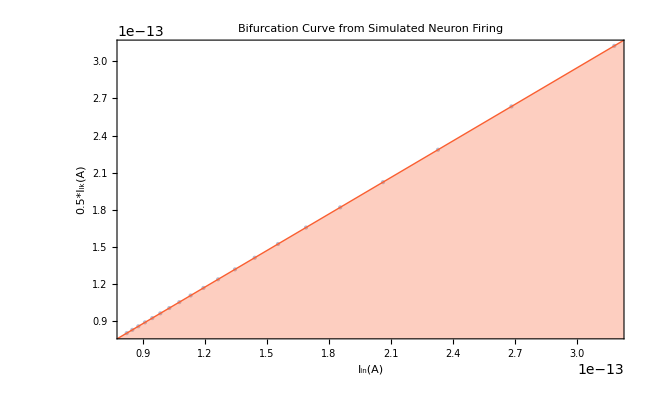

```mathematica
ImValsLPF={
318.187,268.41,232.852,206.202,185.492,
168.941,155.399,144.113,134.563,126.377,
119.282,113.085,107.616,102.755,98.4149,
94.5080,90.9736,87.7603,84.8339,82.1513
}*10^-15;
IinVals={
312.485,263.568,228.627,202.443,182.096,
165.819,152.516,141.431,132.051,124.011,
117.055,110.968,105.597,100.823,96.5599,
92.7234,89.2524,86.0969,83.2231,80.5888
}*10^-15;
dataIinCompare=Transpose[{ImValsLPF,IinVals}];
IinFitEq=Fit[dataIinCompare,{x},x]
IinFitOffEq=Fit[dataIinCompare,{1,x},x]
IinFitRules=FindFit[dataIinCompare,mLPF x,{mLPF},x];
IinFitOffRules=FindFit[dataIinCompare,mOffLPF x+bLPF,{mOffLPF,bLPF},x];
Show[
ListPlot[dataIinCompare,ImageSize->imgSizer,PlotStyle->dataStyle⟦1⟧,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}}],
Plot[IinFitOffEq,{x,0,4*10^-13},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.3],dataStyle⟦4⟧]]
]
```

### ρ_qua bifurcation plot as gotten from the SPICE simulation of a Soma with VCVSources on the biases

This series of data is to measure the bifurcation line using a VCVS to see whether or not and/or how the ringing might affect the measurements.  Observationally, using VCVS definitely increases the firing rate, but not by a great deal.  With a simulation time of 10s, and precision of ι_in down to the 10thousandths, the degree of this increase doesn’t change the bifurcation current of I_in.

```mathematica
IlkBaseVCVS=338.994*10^-15;
IinValsVCVS={
312.485,263.568,228.627,202.443,182.096,
165.819,152.516,141.431,132.051,124.011,
117.055,110.968,105.597,100.823,96.5599,
92.7234,89.2524,86.0969,83.2231,80.5817
}*10^-15;
IlkValsVCVS={
IlkBaseVCVS/0.5,IlkBaseVCVS/0.6,IlkBaseVCVS/0.7,IlkBaseVCVS/0.8,IlkBaseVCVS/0.9,
IlkBaseVCVS/1.0,IlkBaseVCVS/1.1,IlkBaseVCVS/1.2,IlkBaseVCVS/1.3,IlkBaseVCVS/1.4,
IlkBaseVCVS/1.5,IlkBaseVCVS/1.6,IlkBaseVCVS/1.7,IlkBaseVCVS/1.8,IlkBaseVCVS/1.9,
IlkBaseVCVS/2.0,IlkBaseVCVS/2.1,IlkBaseVCVS/2.2,IlkBaseVCVS/2.3,IlkBaseVCVS/2.4};
dataValsVCVS=Transpose[{IinValsVCVS,0.5*IlkValsVCVS}];
dataValsVCVS⟦;;,1⟧/dataValsVCVS⟦;;,2⟧;
pQuaFitEqVCVS=Fit[dataValsVCVS,{x},x];
pQuaFitOffEqVCVS=Fit[dataValsVCVS,{1,x},x];
pQuaFitRulesVCVS=FindFit[dataValsVCVS,mVCVS x,{mVCVS},x];
pQuaFitOffRulesVCVS=FindFit[dataValsVCVS,mOffVCVS x+bVCVS,{mOffVCVS,bVCVS},x];
Print[Style["ρ_qua with no offset: ",Bold],mVCVS/.pQuaFitRulesVCVS]
Print[Style["ρ_qua if offset is included: ",Bold],mOffVCVS/.pQuaFitOffRulesVCVS]
Print[Style["Total Offset: ",Bold],UnitConvert[Quantity[bVCVS,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVS]
Manipulate[
Show[
ListPlot[dataValsVCVS,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle⟦1⟧,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEqVCVS,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.3],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua with no offset: 1.02592

ρ_qua if offset is included: 1.15749

Total Offset: -22.5325

```mathematica
iInValsVCVS={.4609,.4665,.4721,.47775,.48345,.48915,.4949,.50065,.5064,.51215,.51795,.52375,.52955,.53535,.5412,.54705,.5529,.55875,.56465,.5705};
Differences[iInValsVCVS]
```

{0.0056,0.0056,0.00565,0.0057,0.0057,0.00575,0.00575,0.00575,0.00575,0.0058,0.0058,0.0058,0.0058,0.00585,0.00585,0.00585,0.00585,0.0059,0.00585}

```mathematica
Accumulate[{.4609,.0056,.0056,.00565,.0057,.00575,.00575,.00575,.00575,.00575,.00575,0.0058,0.0058,0.0058,0.00585,0.00585,0.00585,0.00585,0.0059,0.0059}]
```

{0.4609,0.4665,0.4721,0.47775,0.48345,0.4892,0.49495,0.5007,0.50645,0.5122,0.51795,0.52375,0.52955,0.53535,0.5412,0.54705,0.5529,0.55875,0.56465,0.57055}

### ρ_qua bifurcation plot as gotten from the SPICE simulation of a Soma with VCVSources and including the contribution to I_lk gotten from the refractory period circuit.

This data measures the bifurcation line while including the contribution of leakage current due to the refractory period circuit.

```mathematica
IinValsVCVSRef={
312.485,263.568,228.627,202.443,182.096,
165.819,152.516,141.431,132.051,124.011,
117.055,110.968,105.597,100.823,96.5599,
92.7234,89.2524,86.0969,83.2231,80.5888
}*10^-15;
IlkValsVCVSRef={
687.131,574.497,494.040,433.693,386.755,
349.203,318.479,292.873,271.206,252.634,
236.538,222.453,210.025,198.978,189.094,
180.197,172.148,164.830,158.149,152.024
}*10^-15;
dataValsVCVSRef=Transpose[{IinValsVCVSRef,0.5*IlkValsVCVSRef}];
dataValsVCVSRef⟦;;,1⟧/dataValsVCVSRef⟦;;,2⟧;
pQuaFitEqVCVSRef=Fit[dataValsVCVSRef,{x},x];
pQuaFitOffEqVCVSRef=Fit[dataValsVCVSRef,{1,x},x];
pQuaFitRulesVCVSRef=FindFit[dataValsVCVSRef,mVCVSRef x,{mVCVSRef},x];
pQuaFitOffRulesVCVSRef=FindFit[dataValsVCVSRef,mOffVCVSRef x+bVCVSRef,{mOffVCVSRef,bVCVSRef},x];
Print[Style["ρ_qua with no offset: ",Bold],mVCVSRef/.pQuaFitRulesVCVSRef]
Print[Style["ρ_qua if offset is included: ",Bold],mOffVCVSRef/.pQuaFitOffRulesVCVSRef]
Print[Style["Total Offset: ",Bold],UnitConvert[Quantity[bVCVSRef,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVSRef]
Manipulate[
Show[
ListPlot[dataValsVCVSRef,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle⟦1⟧,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEqVCVSRef,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.3],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua with no offset: 1.05557

ρ_qua if offset is included: 1.154

Total Offset: -16.8561

```mathematica
iInValsVCVSRef={.4609,.4665,.4721,.47775,.48345,.4892,.49495,.5007,.50645,.5122,.51795,.52375,.52955,.53535,.5412,.54705,.5529,.55875,.56465,.5705};
Differences[iInValsVCVSRef]
```

{0.0056,0.0056,0.00565,0.0057,0.00575,0.00575,0.00575,0.00575,0.00575,0.00575,0.0058,0.0058,0.0058,0.00585,0.00585,0.00585,0.00585,0.0059,0.00585}

```mathematica
Accumulate[{.4609,.0056,.0056,.00565,.0057,.00575,.00575,.00575,.00575,.00575,.00575,0.0058,0.0058,0.0058,0.00585,0.00585,0.00585,0.00585,0.0059,0.0059}]
```

{0.4609,0.4665,0.4721,0.47775,0.48345,0.4892,0.49495,0.5007,0.50645,0.5122,0.51795,0.52375,0.52955,0.53535,0.5412,0.54705,0.5529,0.55875,0.56465,0.57055}

### ρ_qua bifurcation plot as gotten from the SPICE simulation of a Soma with VCVSources, without the I_an circuit, but still including I_lk gotten from the refractory period circuit

This data measures the bifurcation line of the circuit with no V_an circuitry.  Like the previous section, it also includes the contribution to I_lk that is a result of the refractory period.  The I_lk currents are measured on the circuit side, as opposed to the bias side.  With that said, the I_in currents are measured on the bias side, b/c the Soma circuitry results in I_m currents that are much greater than the I_in value b/c of the feedback circuitry.

```mathematica
IinValsVCVSNoVan={
301.908,253.003,218.094,191.934,171.606,
155.344,142.054,130.979,121.608,113.587,
106.636,100.565,95.2075,90.4455,86.1848,
82.3586,78.8968,75.7498,72.8763,70.2494
}*10^-15;
IlkValsVCVSNoVan={
687.133,574.499,494.041,433.694,386.756,
349.204,318.478,292.872,271.205,252.632,
236.536,222.451,210.023,198.976,189.090,
180.194,172.145,164.827,158.145,152.020
}*10^-15;
dataValsVCVSNoVan=Transpose[{IinValsVCVSNoVan,0.5*IlkValsVCVSNoVan}];
dataValsVCVSNoVan⟦;;,1⟧/dataValsVCVSNoVan⟦;;,2⟧;
pQuaFitEqVCVSNoVan=Fit[dataValsVCVSNoVan,{x},x];
pQuaFitOffEqVCVSNoVan=Fit[dataValsVCVSNoVan,{1,x},x];
pQuaFitRulesVCVSNoVan=FindFit[dataValsVCVSNoVan,mVCVSNoVan x,{mVCVSNoVan},x];
pQuaFitOffRulesVCVSNoVan=FindFit[dataValsVCVSNoVan,mOffVCVSNoVan x+bVCVSNoVan,{mOffVCVSNoVan,bVCVSNoVan},x];
Print[Style["ρ_qua if offset is included: ",Bold,15],mOffVCVSNoVan/.pQuaFitOffRulesVCVSNoVan]
Print[Style["Total Offset: ",Bold,15],UnitConvert[Quantity[bVCVSNoVan,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVSNoVan]
Manipulate[
Show[
ListPlot[dataValsVCVSNoVan,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEqVCVSNoVan,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.2],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua if offset is included: 1.15529

Total Offset: -4.9895

```mathematica
iInValsVCVSNoVan={
0.4453,0.4478,0.45035,0.45295,0.4556,
0.45825,0.46095,0.46365,0.46635,0.4691,
0.47185,0.47465,0.47745,0.48025,0.48305,
0.4859,0.48875,0.4916,0.49445,0.49735};
Differences[iInValsVCVSNoVan]
```

{0.0025,0.00255,0.0026,0.00265,0.00265,0.0027,0.0027,0.0027,0.00275,0.00275,0.0028,0.0028,0.0028,0.0028,0.00285,0.00285,0.00285,0.00285,0.0029}

```mathematica
Accumulate[{
0.4453,0.0025,0.00255,0.0026,0.00265,
0.00265,0.0027,0.0027,0.0027,0.00275,
0.00275,0.0028,0.0028,0.0028,0.0028,
0.00285,0.00285,0.00285,0.00285,0.0029}]
```

{0.4453,0.4478,0.45035,0.45295,0.4556,0.45825,0.46095,0.46365,0.46635,0.4691,0.47185,0.47465,0.47745,0.48025,0.48305,0.4859,0.48875,0.4916,0.49445,0.49735}

### ρ_qua bifurcation plot as gotten from the SPICE simulation of a Soma with VCVSources, without the I_an circuit or Series Transistor (M62), but still including I_lk gotten from the refractory period circuit

This data measures the bifurcation line of the circuit with no V_an circuitry and transistor M62 is also removed.  M62 is the switch that disconnects the path from the cap to the leakage currents.  Like the previous two sections, it also includes the contribution to I_lk that is a result of the refractory period.  The I_lk currents are measured on the circuit side, as opposed to the bias side.  With that said, the I_in currents are measured on the bias side, b/c the Soma circuitry results in I_m currents that are much greater than the I_in value b/c of the feedback circuitry.

```mathematica
IinValsVCVSNoVanNoM62={
301.908,253.003,218.094,191.934,171.606,
155.344,142.038,130.979,121.608,113.587,
106.636,100.565,95.2075,90.4455,86.1848,
82.3586,78.8968,75.7498,72.8763,70.2494
}*10^-15;
IlkValsVCVSNoVanNoM62={
687.133,574.499,494.041,433.694,386.756,
349.204,318.478,292.872,271.205,252.632,
236.536,222.451,210.023,198.975,189.090,
180.193,172.144,164.826,158.144,152.019
}*10^-15;
dataValsVCVSNoVanNoM62=Transpose[{IinValsVCVSNoVanNoM62,0.5*IlkValsVCVSNoVanNoM62}];
dataValsVCVSNoVanNoM62⟦;;,1⟧/dataValsVCVSNoVanNoM62⟦;;,2⟧;
pQuaFitEqVCVSNoVanNoM62=Fit[dataValsVCVSNoVanNoM62,{x},x];
pQuaFitOffEqVCVSNoVanNoM62=Fit[dataValsVCVSNoVanNoM62,{1,x},x];
pQuaFitRulesVCVSNoVanNoM62=FindFit[dataValsVCVSNoVanNoM62,mVCVSNoVanNoM62 x,{mVCVSNoVanNoM62},x];
pQuaFitOffRulesVCVSNoVanNoM62=FindFit[dataValsVCVSNoVanNoM62,mOffVCVSNoVanNoM62 x+bVCVSNoVanNoM62,{mOffVCVSNoVanNoM62,bVCVSNoVanNoM62},x];
Print[Style["ρ_qua if offset is included: ",Bold,15],mOffVCVSNoVanNoM62/.pQuaFitOffRulesVCVSNoVanNoM62]
Print[Style["Total Offset: ",Bold,15],UnitConvert[Quantity[bVCVSNoVanNoM62,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVSNoVanNoM62]
Manipulate[
Show[
ListPlot[dataValsVCVSNoVanNoM62,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEqVCVSNoVanNoM62,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.2],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua if offset is included: 1.1553

Total Offset: -4.98927

```mathematica
iInValsVCVSNoVanNoM62={
0.4453,0.4478,0.45035,0.45295,0.4556,
0.45825,0.4609,0.46365,0.46635,0.4691,
0.47185,0.47465,0.47745,0.48025,0.48305,
0.4859,0.48875,0.4916,0.49445,0.49735};
Differences[iInValsVCVSNoVanNoM62]
```

{0.0025,0.00255,0.0026,0.00265,0.00265,0.00265,0.00275,0.0027,0.00275,0.00275,0.0028,0.0028,0.0028,0.0028,0.00285,0.00285,0.00285,0.00285,0.0029}

```mathematica
Accumulate[{
0.4453,0.0025,0.00255,0.0026,0.00265,
0.00265,0.00265,0.0027,0.0027,0.00275,
0.00275,0.0028,0.0028,0.0028,0.0028,
0.00285,0.00285,0.00285,0.00285,0.0029}]
```

{0.4453,0.4478,0.45035,0.45295,0.4556,0.45825,0.4609,0.4636,0.4663,0.46905,0.4718,0.4746,0.4774,0.4802,0.483,0.48585,0.4887,0.49155,0.4944,0.4973}

### ρ_qua bifurcation plot as gotten from the SPICE simulation of a Soma with VCVSources, without the I_an circuit or Series Transistor (M62), but still including I_lk gotten from the refractory period circuit. Longer Simulation, 100 seconds, to find bifurcation point

This data measures the bifurcation line of the circuit with no V_an circuitry and transistor M62 is also removed.  M62 is the switch that disconnects the path from the cap to the leakage currents.  Like the previous two sections, it also includes the contribution to I_lk that is a result of the refractory period.  The I_lk currents are measured on the circuit side, as opposed to the bias side.  With that said, the I_in currents are measured on the bias side, b/c the Soma circuitry results in I_m currents that are much greater than the I_in value b/c of the feedback circuitry.  This section is the exact same test as the previous section, but it measures each simulation for 100seconds, instead of just 10 seconds.  In other words, now anything that has less than 0.1Hz firing rate is considered as not firing, whereas before it was 0.1Hz.  Although the bifurcation line does shift further to the left/upwards, it doesn’t move by much.  The slope is also, ever so trivially closer to 1.

```mathematica
IinValsVCVSNoVanNoM62={
301.908,253.003,218.094,191.934,171.587,
155.327,142.038,130.965,121.595,113.575,
106.625,100.544,95.1875,90.4266,86.1669,
82.3416,78.8726,75.7266,72.8542,70.2283
}*10^-15;
IinValsVCVSNoVanNoM62Prime={
302.838,253.772,218.751,192.507,172.097,
155.785,142.455,131.347,121.949,113.905,
106.934,100.834,95.4624,90.6874,86.4152,
82.5784,79.0996,75.9444,73.0638,70.4300
}*10^-15;
IlkValsVCVSNoVanNoM62={
687.135,574.500,494.041,433.694,386.756,
349.204,318.478,292.872,271.205,252.632,
236.536,222.451,210.022,198.975,189.090,
180.194,172.144,164.826,158.144,152.020
}*10^-15;
dataValsVCVSNoVanNoM62=Transpose[{IinValsVCVSNoVanNoM62,0.5*IlkValsVCVSNoVanNoM62}];
dataValsVCVSNoVanNoM62⟦;;,1⟧/dataValsVCVSNoVanNoM62⟦;;,2⟧;
pQuaFitEqVCVSNoVanNoM62=Fit[dataValsVCVSNoVanNoM62,{x},x];
pQuaFitOffEqVCVSNoVanNoM62=Fit[dataValsVCVSNoVanNoM62,{1,x},x];
pQuaFitRulesVCVSNoVanNoM62=FindFit[dataValsVCVSNoVanNoM62,mVCVSNoVanNoM62 x,{mVCVSNoVanNoM62},x];
pQuaFitOffRulesVCVSNoVanNoM62=FindFit[dataValsVCVSNoVanNoM62,mOffVCVSNoVanNoM62 x+bVCVSNoVanNoM62,{mOffVCVSNoVanNoM62,bVCVSNoVanNoM62},x];
Print[Style["ρ_qua with no offset: ",Bold,15],mVCVSNoVanNoM62/.pQuaFitRulesVCVSNoVanNoM62]
Print[Style["ρ_qua if offset is included: ",Bold,15],mOffVCVSNoVanNoM62/.pQuaFitOffRulesVCVSNoVanNoM62]
Print[Style["Total Offset: ",Bold,15],UnitConvert[Quantity[bVCVSNoVanNoM62,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVSNoVanNoM62]
Manipulate[
Show[
ListPlot[dataValsVCVSNoVanNoM62,ImageSize->imgSizer,PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->dataStyle,FrameLabel->{Style["I_in(A)",Medium,FontFamily->"Helvetica"],Style["0.5*I_lk(A)",Medium,FontFamily->"Helvetica"]},Frame->True,LabelStyle->Directive[FontTracking->"Plain", FontSize->8],PlotLabel->Style["Bifurcation Curve from Simulated Neuron Firing",13,FontTracking->"Plain"],ImagePadding->{{80,30},{50,10}},AxesOrigin->{xMin,yMin}],
(*Plot[pQuaFitEq,{x,0,xMax},Filling->0,PlotStyle->dataStyle⟦5⟧,FillingStyle->Directive[Opacity[0.3],dataStyle⟦5⟧]],*)
Plot[pQuaFitOffEqVCVSNoVanNoM62,{x,0,xMax},PlotStyle->dataStyle⟦4⟧,Filling->Bottom,FillingStyle->Directive[Opacity[0.2],dataStyle⟦4⟧]]
],
{{xMin,0},0.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled","Open"}},
{{xMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13 ,Appearance->{"Labeled", "Open"}},
{{yMin,-4.*10^-14},-1.*10^-13,10.*10^-13 ,0.1*10^-13,Appearance->{"Labeled", "Open"}},
{{yMax,3.5*10^-13},1.*10^-13,10.*10^-13,0.1*10^-13, Appearance->{"Labeled", "Open"}}]
```

ρ_qua with no offset: 1.12475

ρ_qua if offset is included: 1.15517

Total Offset: -4.95685

```mathematica
iInValsVCVSNoVanNoM62={
0.4453,0.4478,0.45035,0.45295,0.45555,
0.4582,0.4609,0.4636,0.4663,0.46905,
0.4718,0.47455,0.47735,0.48015,0.48295,
0.4858,0.4886,0.49145,0.4943,0.4972};
Differences[iInValsVCVSNoVanNoM62]
Accumulate[{
0.4453,0.0025,0.00255,0.0026,0.00265,
0.00265,0.00265,0.0027,0.0027,0.00275,
0.00275,0.0028,0.0028,0.0028,0.0028,
0.00285,0.00285,0.00285,0.00285,0.0029}]
```

{0.0025,0.00255,0.0026,0.0026,0.00265,0.0027,0.0027,0.0027,0.00275,0.00275,0.00275,0.0028,0.0028,0.0028,0.00285,0.0028,0.00285,0.00285,0.0029}

{0.4453,0.4478,0.45035,0.45295,0.4556,0.45825,0.4609,0.4636,0.4663,0.46905,0.4718,0.4746,0.4774,0.4802,0.483,0.48585,0.4887,0.49155,0.4944,0.4973}

#### Validation Bifurcation values for ι_in

Using the values that were extracted for ρ_qua and offset, the bifurcation points are double checked for I_in.  The values below are the new bifurcation values when I_in is calculated as I_in=((ι_in I_lk)-b)/ρ_qua with ρ_qua=1.15517 and b=-4.95685f

```mathematica
ArrayReshape[Join[{0},Differences[{
.5071,.5085,.5100,.51155,.5131,
.5147,.51635,.5180,.51965,.52135,
.5231,.5248,.52655,.5283,.53005,
.5319,.53375,.53555,.5374,.53925
}]],{4,5}]
ArrayReshape[Accumulate[{
0.5071,0.0014,0.0015,0.00155,0.00155,
0.0016,0.00165,0.00165,0.00165,0.0017,
0.00175,0.0017,0.00175,0.00175,0.00175,
0.00185,0.00185,0.0018,0.00185,0.00185
}],{4,5}]
```

(0 | 0.0014 | 0.0015 | 0.00155 | 0.00155
0.0016 | 0.00165 | 0.00165 | 0.00165 | 0.0017
0.00175 | 0.0017 | 0.00175 | 0.00175 | 0.00175
0.00185 | 0.00185 | 0.0018 | 0.00185 | 0.00185)

(0.5071 | 0.5085 | 0.51 | 0.51155 | 0.5131
0.5147 | 0.51635 | 0.518 | 0.51965 | 0.52135
0.5231 | 0.5248 | 0.52655 | 0.5283 | 0.53005
0.5319 | 0.53375 | 0.53555 | 0.5374 | 0.53925)

## Appendix

```mathematica
h[Vin_]:=(π+2ArcCot[√(-1+2Vin)])/(√(-1+2Vin))
```

```mathematica
((UnitConvert[Quantity[bVCVS,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVS)-(UnitConvert[Quantity[bVCVSRef,"Amps"],"FemtoAmps"]/.pQuaFitOffRulesVCVSRef))*2
```

-11.3527

### Function Definitions

#### GetData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
GetData[fileName_]:=Module[{tauVals,iInVals,data,i},
i=Import[fileName,"Data"];
tauVals=Rest[i⟦1⟧];
iInVals =Rest[i⟦;;,1⟧];
data=i⟦2;;,2;;⟧;
Clear[i];
Return[{tauVals,iInVals, data}];
](* GetData Module *)
```

### Color Chooser (gotten from SomaPTauCalc.nb)

Vary the index value of ColorData and see new colors appear.  These values once set change the colors used in the plot.

```mathematica
dataStyle=Riffle[ColorData[55,"ColorList"],ColorData[31,"ColorList"]];
dashedStyle=Tuples[{{Dashed}, dataStyle}];
boldStyle=Tuples[{{Thick}, dataStyle}];
Graphics[{#,PointSize[1],Point[{0,0}]},ImageSize-> 30]&/@dataStyle
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}